## Common Elements

```mathematica
Needs["HEPMath`"]
DeclareLorentzVectors[l,_p];
```

DeclareHEPTensor::redecl: HEPTensor l already declared.

```mathematica
f1=m@1^2-m@0^2-Sqr[p@1];
f2=m@2^2-m@1^2-Sqr[p@1+p@2]+Sqr[p@1];
f3=m@3^2-m@2^2-Sqr[p@1+p@2+p@3]+Sqr[p@1+p@2];

argsB=argsB01=Sequence[p@1,m@0,m@1];
argsB02=Sequence[p@1+p@2,m@0,m@2];
argsB03=Sequence[p@1+p@2+p@3,m@0,m@3];
argsB12=Sequence[p@2,m@1,m@2];
argsB13=Sequence[p@2+p@3,m@1,m@3];
argsB23=Sequence[p@3,m@2,m@3];
argsC=argsC012=Sequence[p@1,p@2,m@0,m@1,m@2];
argsC013=Sequence[p@1,p@2+p@3,m@0,m@1,m@3];
argsC023=Sequence[p@1+p@2,p@3,m@0,m@2,m@3];
argsC123=Sequence[p@2,p@3,m@1,m@2,m@3];
argsD=Sequence[p@1,p@2,p@3,m@0,m@1,m@2,m@3];
```

```mathematica
repVecs={
Sqr[p@1]-> p12,Sqr[p@2]-> p22,Sqr[p@3]-> p32,
SDot[p@1,p@2]-> sp12,SDot[p@1,p@3]-> sp13,SDot[p@2,p@3]-> sp23,
SDot[p@1+p@2,p@3]-> sp13+sp23,SDot[p@1,p@2+p@3]-> sp12+sp13,
Sqr[p@1+p@2]-> p12+p22+2sp12,Sqr[p@1+p@3]-> p12+p32+2sp13,Sqr[p@2+p@3]-> p22+p32+2sp23,
Sqr[p@1+p@2+p@3]-> p12+p22+p32+2sp12+2sp13+2sp23
};
Module[{l,t},Do[l=HEPExpand[First@e]/.repVecs;t=Simplify[l-Last@e];If[Not[t===0],Print[e, "is not consinstent! ",l]],{e,repVecs}]]
repMasses={m@0-> Sqrt@m02,m@1-> Sqrt@m12,m@2-> Sqrt@m22,m@3-> Sqrt@m32};
cmp[a_,b_]:=Simplify[Expand[(a-b)//.repVecs//.repMasses/.{Dim->4+ϵ}]];
getScalars[x_]:=Module[{l},
l=Reap[x/.{
rA[0][a__]:> Sow[rA[0][a]],
rB[0][a__]:> Sow[rB[0][a]],
rC[0][a__]:> Sow[rC[0][a]],
rD[0][a__]:> Sow[rD[0][a]]
}];
DeleteDuplicates[l[[2,1]]]
];
cmp2[a_,b_]:=Module[{x,y,l,lx,ly,ls,l2},
x=Expand[a//.repVecs//.repMasses/.{Dim->4+ϵ}];
y=Expand[b//.repVecs//.repMasses/.{Dim->4+ϵ}];
l=getScalars[x];
lx=CoefficientList[x,l];
ly=CoefficientList[y,l];
If[Dimensions[lx]≠Dimensions[ly],Return[$Failed]];
ls=Simplify[lx-ly];
l2=Reap[MapIndexed[{e,ind}↦If[Not[0==e],Sow[{ind,e}]],ls,{Length@l}]];
l2=l2[[2]];
If[Length@l2==0,0,{l,l2[[1]]}]
]
collectScalars[x_]:=collectScalars[x,e↦Normal@Series[Simplify@HEPExpand[e/.{Dim->4+ϵ}],{ϵ,0,1}]]
collectScalars[x_,f_Function]:=Collect[x,getScalars[x],f]
```

## Passarino-Veltman Decomposition

### bubble functions B

```mathematica
Clear[rB];
SetAttributes[rB,Orderless];

rB[1]={q,m0,m1}↦Evaluate[collectScalars[(1/(2Sqr[p@1])(f1 rB[0][argsB]+rA[0][m@0]-rA[0][m@1]))]/.{p@1-> q,m@0-> m0,m@1-> m1}];
rB[0,0]={q,m0,m1}↦Evaluate[collectScalars[(1/(2(Dim-1))(2m@0^2 rB[0][argsB]+rA[0][m@1]-f1 rB[1][argsB]))]/.{p@1-> q,m@0-> m0,m@1-> m1}];
rB[1,1]={q,m0,m1}↦Evaluate[collectScalars[(1/(2Sqr[p@1])(f1 rB[1][argsB]+rA[0][m@1]-2rB[0,0][argsB]))]/.{p@1-> q,m@0-> m0,m@1-> m1}];
```

### triangle functions C

```mathematica
Xc=Table[SDot[p[j],p[k]],{j,2},{k,2}];
iXc=Inverse@Xc;
SetAttributes[rC,Orderless];
```

```mathematica
Module[{S,i},
S={
1/2(f1 rC[0][argsC]+rB[0][argsB02]-rB[0][argsB12]), (* =Subscript[R, 1] *)
1/2(f2 rC[0][argsC]+rB[0][argsB01]-rB[0][argsB02])  (* =Subscript[R, 2] *)
};
i=iXc.S;
rC[1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
]
```

```mathematica
Module[{S00,S11,S12,S21,S22,i1,i2,t},
S00=rB[0][argsB12]+m@0^2 rC[0][argsC];
S11=1/2(f1 rC[1][argsC]+rB[1][argsB02]+rB[0][argsB12]); (* =Subscript[R, 3] *)
S12=1/2(f2 rC[1][argsC]+rB[1][argsB01]-rB[1][argsB02]); (* =Subscript[R, 4] *)
S21=1/2(f1 rC[2][argsC]+rB[1][argsB02]-rB[1][argsB12]); (* =Subscript[R, 5] *)
S22=1/2(f2 rC[2][argsC]-rB[1][argsB02]); (* =Subscript[R, 6] *)

rC[0,0]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[(1/(Dim-2)(S00-S11-S22))]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
i1=iXc.{S11-rC[0,0][argsC],S12};
rC[1,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[1,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
i2=iXc.{S21,S22-rC[0,0][argsC]};
rC[2,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i2[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];

Print["cross check C_21: ",cmp2[i2[[1]],rC[2,1][argsC]]];
]
```

cross check C_21: 0

```mathematica
Module[{S,i0,i1,i2},
S[0,0,1]=1/2(f1 rC[0,0][argsC]+rB[0,0][argsB02]-rB[0,0][argsB12]); (* =Subscript[R, 10] *)
S[0,0,2]=1/2(f2 rC[0,0][argsC]+rB[0,0][argsB01]-rB[0,0][argsB02]); (* =Subscript[R, 11] *)
i0 = iXc.{S[0,0,1],S[0,0,2]};
rC[0,0,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i0[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[0,0,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i0[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];

S[1,1,1]=1/2(f1 rC[1,1][argsC]+rB[1,1][argsB02]-rB[0][argsB12]); (* =Subscript[R, 12] *)
S[1,1,2]=1/2(f2 rC[1,1][argsC]+rB[1,1][argsB01]-rB[1,1][argsB02]); (* =Subscript[R, 13] *)
i1 = iXc.{S[1,1,1]-2rC[0,0,1][argsC],S[1,1,2]};
rC[1,1,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[1,1,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i1[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];

S[2,2,1]=1/2(f1 rC[2,2][argsC]+rB[1,1][argsB02]-rB[1,1][argsB12]); (* =Subscript[R, 14] *)
S[2,2,2]=1/2(f2 rC[2,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 15] *)
i2 = iXc.{S[2,2,1],S[2,2,2]-2rC[0,0,2][argsC]};
rC[2,2,1]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i2[[1]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
rC[2,2,2]={q1,q2,m0,m1,m2}↦Evaluate[collectScalars[i2[[2]]]/.{p@1-> q1,p@2-> q2,m@0-> m0,m@1-> m1,m@2-> m2}];
]
```

```mathematica
Module[{S,i12},
S[1,2,1]=1/2(f1 rC[1,2][argsC]+rB[1,1][argsB02]+rB[1][argsB12]); (* =Subscript[R, 16] *)
S[1,2,2]=1/2(f2 rC[1,2][argsC]-rB[1,1][argsB02]); (* =Subscript[R, 17] *)
i12 = iXc.{S[1,2,1]-rC[0,0,2][argsC],S[1,2,2]-rC[0,0,1][argsC]};
Print["cross check C_121: ",cmp2[i12[[1]],rC[1,1,2][argsC]]];
Print["cross check C_122: ",cmp2[i12[[2]],rC[1,2,2][argsC]]];
]
```

cross check C_121: 0

cross check C_122: 0

### box function D

```mathematica
Xd=Table[SDot[p[j],p[k]],{j,3},{k,3}];
iXd=Inverse@Xd;
SetAttributes[rD,Orderless];
```

```mathematica
Module[{T,i},
T={
1/2(f1 rD[0][argsD]+rC[0][argsC023]-rC[0][argsC123]), (* =Subscript[R, 20] *)
1/2(f2  rD[0][argsD]+rC[0][argsC013]-rC[0][argsC023]), (* =Subscript[R, 21] *)
1/2(f3  rD[0][argsD]+rC[0][argsC012]-rC[0][argsC013]) (* =Subscript[R, 22] *)
};
i=iXd.T;
rD[1]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[1]]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[2]]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[3]]]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
]
```

```mathematica
Module[{T,i1,i2,i3},
T[0,0]=m@0^2 rD[0][argsD]+rC[0][argsC123];

T[1,1]=1/2(f1 rD[1][argsD]+rC[1][argsC023]+rC[0][argsC123]);(* =Subscript[R, 30] *)
T[1,2]=1/2(f2 rD[1][argsD]+rC[1][argsC013]-rC[1][argsC023]);(* =Subscript[R, 31] *)
T[1,3]=1/2(f3 rD[1][argsD]+rC[1][argsC012]-rC[1][argsC013]);(* =Subscript[R, 32] *)

T[2,1]=1/2(f1 rD[2][argsD]+rC[1][argsC023]-rC[1][argsC123]);(* =Subscript[R, 33] *)
T[2,2]=1/2(f2 rD[2][argsD]+rC[2][argsC013]-rC[1][argsC023]); (* =Subscript[R, 34] *)
T[2,3]=1/2(f3 rD[2][argsD]+rC[2][argsC012]-rC[2][argsC013]); (* =Subscript[R, 35] *)

T[3,1]=1/2(f1 rD[3][argsD]+rC[2][argsC023]-rC[2][argsC123]); (* =Subscript[R, 36] *)
T[3,2]=1/2(f2 rD[3][argsD]+rC[2][argsC013]-rC[2][argsC023]); (* =Subscript[R, 37] *)
T[3,3]=1/2(f3 rD[3][argsD]-rC[2][argsC013]); (* =Subscript[R, 38] *)

PrintTemporary[{0,0}];
rD[0,0]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(1/(Dim-3)(T[0,0]-T[1,1]-T[2,2]-T[3,3]))]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary[{1,1}];
i1=iXd.{T[1,1]-rD[0,0][argsD],T[1,2],T[1,3]};
rD[1,1]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i1[[1]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[1,2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i1[[2]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[1,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i1[[3]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary[{2,2}];
i2=iXd.{T[2,1],T[2,2]-rD[0,0][argsD],T[2,3]};
rD[2,2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i2[[2]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];
rD[2,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i2[[3]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary[{3,3}];
i3=iXd.{T[3,1],T[3,2],T[3,3]-rD[0,0][argsD]};
rD[3,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[(i3[[3]])]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3}];

PrintTemporary["Checks"];
Print["cross check D_21: ",cmp2[i2[[1]],rD[2,1][argsD]]];
Print["cross check D_31: ",cmp2[i3[[1]],rD[3,1][argsD]]];
Print["cross check D_32: ",cmp2[i3[[2]],rD[3,2][argsD]]];
]
```

cross check D_21: 0

cross check D_31: 0

cross check D_32: 0

```mathematica
Module[{T,i12,f},
T[0,0,1]=1/2(f1 rD[0,0][argsD]+rC[0,0][argsC023]-rC[0,0][argsC123]); (* =Subscript[R, 40] *)
T[0,0,2]=1/2(f2 rD[0,0][argsD]+rC[0,0][argsC013]-rC[0,0][argsC023]); (* =Subscript[R, 41] *)
T[0,0,3]=1/2(f3 rD[0,0][argsD]+rC[0,0][argsC012]-rC[0,0][argsC013]); (* =Subscript[R, 42] *)

T[1,1,1]=1/2(f1 rD[1,1][argsD]+rC[1,1][argsC023]-rC[0][argsC123]); (* =Subscript[R, 43] *)
T[1,1,2]=1/2(f2 rD[1,1][argsD]+rC[1,1][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 44] *)
T[1,1,3]=1/2(f3 rD[1,1][argsD]+rC[1,1][argsC012]-rC[1,1][argsC013]); (* =Subscript[R, 45] *)

T[2,2,1]=1/2(f1 rD[2,2][argsD]+rC[1,1][argsC023]-rC[1,1][argsC123]); (* =Subscript[R, 46] *)
T[2,2,2]=1/2(f2 rD[2,2][argsD]+rC[2,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 47] *)
T[2,2,3]=1/2(f3 rD[2,2][argsD]+rC[2,2][argsC012]-rC[2,2][argsC013]); (* =Subscript[R, 48] *)

T[3,3,1]=1/2(f1 rD[3,3][argsD]+rC[2,2][argsC023]-rC[2,2][argsC123]); (* =Subscript[R, 49] *)
T[3,3,2]=1/2(f2 rD[3,3][argsD]+rC[2,2][argsC013]-rC[2,2][argsC023]); (* =Subscript[R, 50] *)
T[3,3,3]=1/2(f3 rD[3,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 51] *)

T[1,2,1]=1/2(f1 rD[1,2][argsD]+rC[1,1][argsC023]+rC[1][argsC123]); (* =Subscript[R, 52] *)
T[1,2,2]=1/2(f2 rD[1,2][argsD]+rC[1,2][argsC013]-rC[1,1][argsC023]); (* =Subscript[R, 53] *)
T[1,2,3]=1/2(f3 rD[1,2][argsD]+rC[1,2][argsC012]-rC[1,2][argsC013]); (* =Subscript[R, 54] *)

f=e↦Normal@Series[e/.{Dim->4+ϵ},{ϵ,0,1}];

Do[Module[{v,i},
v={T[n,n,1],T[n,n,2],T[n,n,3]};
If[n>0,v[[n]]-=2rD[0,0,n][argsD]];
i = iXd.v;
PrintTemporary[{n,n,1}];
rD[n,n,1]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[1]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3,Dim->4+ϵ}];
PrintTemporary[{n,n,2}];
rD[n,n,2]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[2]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3,Dim->4+ϵ}];
PrintTemporary[{n,n,3}];
rD[n,n,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i[[3]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3,Dim->4+ϵ}];
],{n,0,3}];

i12= iXd.{T[1,2,1]-rD[0,0,2][argsD],T[1,2,2]-rD[0,0,1][argsD],T[1,2,3]};
PrintTemporary[{1,2,3}];
rD[1,2,3]={q1,q2,q3,m0,m1,m2,m3}↦Evaluate[collectScalars[i12[[3]],f]/.{p@1-> q1,p@2-> q2,p@3-> q3,m@0-> m0,m@1-> m1,m@2-> m2,m@3-> m3,Dim->4+ϵ}];

PrintTemporary["Checks"];
Print["cross check D_121: ",cmp2[i12[[1]],rD[1,2,1][argsD]]];
Print["cross check D_122: ",cmp2[i12[[2]],rD[1,2,2][argsD]]];
]
```

cross check D_121: 0

cross check D_122: 0

```mathematica
Module[{T,i13,i23,a,b},
T[1,3,1]=1/2(f1 rD[1,3][argsD]+rC[1,2][argsC023]+rC[2][argsC123]); (* =Subscript[R, 55] *)
T[1,3,2]=1/2(f2 rD[1,3][argsD]+rC[1,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 56] *)
T[1,3,3]=1/2(f3 rD[1,3][argsD]-rC[1,2][argsC013]); (* =Subscript[R, 57] *)

T[2,3,1]=1/2(f1 rD[2,3][argsD]+rC[1,2][argsC023]-rC[1,2][argsC123]); (* =Subscript[R, 58] *)
T[2,3,2]=1/2(f2 rD[2,3][argsD]+rC[2,2][argsC013]-rC[1,2][argsC023]); (* =Subscript[R, 59] *)
T[2,3,3]=1/2(f3 rD[2,3][argsD]-rC[2,2][argsC013]); (* =Subscript[R, 60] *)

i13= iXd.{T[1,3,1]-rD[0,0,3][argsD],T[1,3,2],T[1,3,3]-rD[0,0,1][argsD]};
i23= iXd.{T[2,3,1],T[2,3,2]-rD[0,0,3][argsD],T[2,3,3]-rD[0,0,2][argsD]};

a=i13[[1]];
b=rD[1,3,1][argsD];

Print["cross check D_131: ",cmp2[i13[[1]],rD[1,3,1][argsD]]];
Print["cross check D_132: ",cmp2[i13[[2]],rD[1,3,2][argsD]]];
Print["cross check D_133: ",cmp2[i13[[3]],rD[1,3,3][argsD]]];
Print["cross check D_231: ",cmp2[i23[[1]],rD[2,3,1][argsD]]];
Print["cross check D_232: ",cmp2[i23[[2]],rD[2,3,2][argsD]]];
Print["cross check D_233: ",cmp2[i23[[3]],rD[2,3,3][argsD]]];
]
```

cross check D_131: 0

cross check D_132: 0

cross check D_133: 0

cross check D_231: 0

cross check D_232: 0

cross check D_233: 0

### Check to Marco

```mathematica
Module[{r,map,a,b,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_C.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],n-> Dim};
map={
c11-> 1,
c12-> 2,
c24->{0,0},
c21-> {1,1},
c22-> {2,2},
c23-> {1,2},
c31-> {1,1,1},
c32-> {2,2,2},
c33-> {1,1,2},
c34-> {1,2,2},
c35-> {0,0,1},
c36-> {0,0,2}
};
Do[
a=((First@e)[argsC]/.r);
b=rC[(Last@e)/.{List-> Sequence}][argsC];
Print@cmp2[a,b];
,{e,map}]
]
```

0

0

0

«9 more identical outputs»

```mathematica
Module[{r,map,a,b,ca,cb,d},
<<"~/Physik/PhD/Marco/PaVe/tensor_D.m";
r={S-> SDot,a0-> rA[0],b0-> rB[0],c0-> rC[0],d0-> rD[0],n-> Dim};
map={
d11-> 1,
d12-> 2,
d13-> 3,
d21-> {1,1},
d22-> {2,2},
d23-> {3,3},
d24-> {1,2},
d25-> {1,3},
d26-> {2,3},
d27-> {0,0},
d31-> {1,1,1},
d32-> {2,2,2},
d33-> {3,3,3},
d34-> {1,1,2},
d35-> {1,1,3},
d36-> {1,2,2},
d37->{1,3,3},
d38-> {2,2,3},
d39->{2,3,3},
d310-> {1,2,3},
d311-> {0,0,1},
d312-> {0,0,2},
d313-> {0,0,3}
};
Do[
a=((First@e)[argsD]/.r);
b=rD[(Last@e)/.{List-> Sequence}][argsD];
Print@cmp2[a,b];
,{e,map}]
]
```

0

0

0

«20 more identical outputs»

### Export

```mathematica
Save["~/Physik/PhD/MMa/data/rT.m",{rB,rC,rD}];
```

```mathematica
<<"~/Physik/PhD/MMa/data/rT.m";
```

## Scalar Integrals

```mathematica
Module[{ls,is},
ls=Flatten[Table[{j,j,k},{j,0,3},{k,3}],1];
is={};
Do[AppendTo[is,getScalars[rD[e/.List->Sequence][p1,-k1,-q,0,m,m,m]]],{e,ls}];
Sort@DeleteDuplicates@Flatten[is,1]
]
```

{rA[0][0],rA[0][m],rB[0][-k1,m,m],rB[0][p1,0,m],rB[0][-k1+p1,0,m],rB[0][-k1-q,m,m],rB[0][-k1+p1-q,0,m],rB[0][-q,m,m],rC[0][-k1,-q,m,m,m],rC[0][p1,-k1,0,m,m],rC[0][p1,-k1-q,0,m,m],rC[0][-k1+p1,-q,0,m,m],rD[0][p1,-k1,-q,0,m,m,m]}

```mathematica
fBeen2Den=(2π)^4/(I π^2)
Cϵ[m2_,μ2_]:=1/(16π^2)Exp[ϵ/2(EulerGamma-Log[4π])](m2/μ2)^(ϵ/2);
```

-16 ⅈ π^2

### A_0

```mathematica
sA0[μ2_][m2]:=Normal@Series[I Cϵ[m2,μ2] m2(-2/ϵ+1),{ϵ,0,0}];
sA0[μ2_][0]:=0;
```

```mathematica
Module[{A0Den},
A0Den=-m2(m2/(4π μ2))^(ϵ/2)Gamma[-1-ϵ/2];
Print@Simplify@Series[A0Den,{ϵ,0,0}];
Print[sA0[μ2][m2]];
Print@FullSimplify[Series[A0Den,{ϵ,0,2}]-Series[fBeen2Den*I Cϵ[m2,μ2] m2(-2/ϵ+1),{ϵ,0,2}]];
]
```

-(2 m2)/ϵ-m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2])+O[ϵ]^1

-(ⅈ m2)/(8 π^2 ϵ)-(ⅈ m2 (-1+EulerGamma-Log[4 π]+Log[m2/μ2]))/(16 π^2)

-1/24 (m2 (12+π^2)) ϵ+1/48 m2 (-EulerGamma (12+π^2)+π^2 (1+Log[4]+Log[π])-(12+π^2) Log[m2/μ2]+4 (3+Log[64]+3 Log[π]-Zeta[3])) ϵ^2+O[ϵ]^3

### B_0

```mathematica
sB0[μ2_][s,m2,m2]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ+2+β Log[χ]),{ϵ,0,0}];
sB0[μ2_][q2,m2,m2]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ+2+βq Log[χq]),{ϵ,0,0}];
sB0[μ2_][0,m2,m2]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ),{ϵ,0,0}];
sB0[μ2_][m2,0,m2]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ+2),{ϵ,0,0}];
sB0[μ2_][t,0,m2]:=Normal@Series[ I Cϵ[m2,μ2](-2/ϵ+2-(t-m2)/t Log[-(t-m2)/m2]),{ϵ,0,0}];
sB0[μ2_][u,0,m2]:=(sB0[μ2][t,0,m2]/.{t-> u});
```

#### Computation

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((2m2-p2)/m2) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m2/μ2]-m2/p2(1/r-r)Log@r;
Print@FullSimplify[B0/.rSol//.{p2-> s,s-> 4m2/ρ,ρ-> 1-β^2},Assumptions-> {0<β<1,m2>0}];
]
```

{{r→-(-2 m2+p2-√(-4 m2 p2+p2^2))/(2 m2)},{r→-(-2 m2+p2+√(-4 m2 p2+p2^2))/(2 m2)}}

{2-EulerGamma-2/ϵ+Log[4]+Log[π]+β Log[(-1+β)/(1+β)]-Log[m2/μ2],2-EulerGamma-2/ϵ+Log[4]+Log[π]-β Log[(1+β)/(-1+β)]-Log[m2/μ2]}

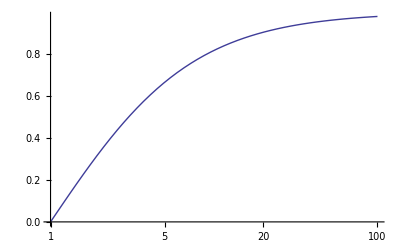

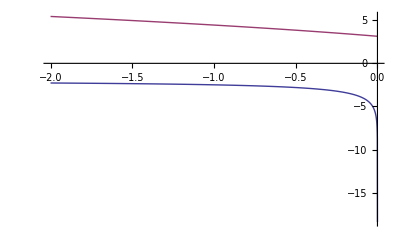

```mathematica
LogLinearPlot[-(1-b)/(1+b),{b,1,100}]
Plot[{Re@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]},Im@(b Log[x])//.{x-> (1-b)/(1+b),b-> Sqrt[1-r]}},{r,-2,0}]
```

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((m0^2+m1^2-p2)/(m0 m1)) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m0 m1/μ2]+(m0^2-m1^2)/p2 Log[m1/m0]-m0 m1/p2(1/r-r)Log@r;
Print@Limit[B0/.rSol/.{m1-> Sqrt@m2,p2-> m2},m0-> 0,Assumptions-> {m2>0}];
]
```

{{r→(m0^2+m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)-p2)/(2 m0 m1)},{r→-(-m0^2-m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)+p2)/(2 m0 m1)}}

{2-EulerGamma-2/ϵ-Log[m2/(4 π μ2)],2-EulerGamma-2/ϵ-Log[m2/(4 π μ2)]}

```mathematica
Module[{rSol,Δ,B0},
Δ=-2/ϵ-EulerGamma+Log[4π];
rSol=Solve[x^2+((m0^2+m1^2-p2)/(m0 m1)) x +1 == (x+r)(x+1/r),r];
Print@rSol;
B0=Δ+2-Log[m0 m1/μ2]+(m0^2-m1^2)/p2 Log[m1/m0]-m0 m1/p2(1/r-r)Log@r;
Print@Expand@Limit[B0/.rSol/.{m1-> Sqrt@m2,p2-> t},m0-> 0,Assumptions-> {t<0,m2>0,t-m2<0}];
]
```

{{r→(m0^2+m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)-p2)/(2 m0 m1)},{r→-(-m0^2-m1^2+√(-4 m0^2 m1^2+(m0^2+m1^2-p2)^2)+p2)/(2 m0 m1)}}

{2-EulerGamma-2/ϵ-(m2 Log[m2])/(2 t)+Log[4 π]-Log[(m2-t)/(√m2)]+(m2 Log[(m2-t)/(√m2)])/t-Log[(√m2)/μ2],2-EulerGamma-2/ϵ+Log[4]-(m2 Log[m2])/t+(m2 Log[m2-t])/t-Log[(m2-t)/(π μ2)]}

### C_0

```mathematica
sC0[μ2_][s,q2,0,m2,m2,m2]:=Normal@Series[I Cϵ[m2,μ2]/(s-q2)(1/2 Log[χ]^2-1/2 Log[χq]^2-3zeta2),{ϵ,0,0}];
sC0[μ2_][0,q2,s,m2,m2,m2]:=sC0[μ2][s,q2,0,m2,m2,m2]
sC0[μ2_][s,0,0,m2,m2,m2]:=Normal@Series[I Cϵ[m2,μ2]/(s-q2)(1/2 Log[χ]^2-3zeta2),{ϵ,0,0}];
sC0[μ2_][m2,0,t,0,m2,m2]:=Normal@Series[I Cϵ[m2,μ2]/(t-m2)(zeta2-PolyLog[2,t/m2]),{ϵ,0,0}];
sC0[μ2_][m2,0,u,0,m2,m2]:=(sC0[μ2][m2,0,t,0,m2,m2]/.{t-> u});
sC0[μ2_][m2,s,m2,0,m2,m2]:=Normal@Series[(I Cϵ[m2,μ2]/(s β)(-2/ϵ Log[χ]-2Log[χ]Log[1-χ]-2PolyLog[2,χ]+1/2Log[χ]^2-4zeta2)),{ϵ,0,0}];
sC0[μ2_][t,m2,q2,0,m2,m2]:=Normal@Series[I Cϵ[m2,μ2]((1/(Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))(
-zeta2+2 PolyLog[2,-((-m2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])/(m2-t))]+
PolyLog[2,(m2-q2+t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])/(m2-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])]+ PolyLog[2,(q2 (-3 m2+q2-t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(-3 m2 q2+q2^2-q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))])]- PolyLog[2,(q2 (-3 m2+q2-t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(-3 m2 q2+q2^2-q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))])]+ PolyLog[2,-((q2 (-3 m2+q2-t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(3 m2 q2-q2^2+q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))]))]- PolyLog[2,-((q2 (-3 m2+q2-t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/(3 m2 q2-q2^2+q2 t+Sqrt[q2 (-4 m2+q2) (m2^2+(q2-t)^2-2 m2 (q2+t))]))]- PolyLog[2,(m2^2-m2 (q2+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])-t (-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/((m2-t) (m2-q2+t-Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))]- PolyLog[2,(m2^2-m2 (q2+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)])-t (-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))/((m2-t) (m2-q2+t+Sqrt[m2^2+(q2-t)^2-2 m2 (q2+t)]))])),{ϵ,0,0}];
sC0[μ2_][u,m2,q2,0,m2,m2]:=(sC0[μ2][t,m2,q2,0,m2,m2]/.{t-> u});
sC0[μ2_][m2,q2,u,0,m2,m2]:=sC0[μ2][u,m2,q2,0,m2,m2];
sC0[μ2_][u,q2,m2,0,m2,m2]:=sC0[μ2][u,m2,q2,0,m2,m2];
```

```mathematica
κ[x_,y_,z_]:=Sqrt[x^2+y^2+z^2-2(x y +y z + z x)];
Series[κ[x2,m2,m2],{x2,0,1}]
```

2 √-m2 √x2+O[x2]^(3/2)

#### Computing C_0(s,q.b2,0,m.b2,m.b2,m.b2)

```mathematica
Limit[-PolyLog[2,2/(1-b)]-PolyLog[2,2/(1+b)],b-> ∞,Assumptions-> {m2>0}]
Limit[-PolyLog[2,(2 q2)/(q2-√(q2 (-4 m2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 m2+q2)))],q2-> 0,Assumptions-> {m2>0}]
```

0

0

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C},
p2[1]=p2[1,0]=s;
p2[2]=p2[2,0]=k2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
Print@Limit[αα,k2-> 0,Assumptions-> {s>0,s-q2>0}];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print[{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print@α[i];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print[{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print@Limit[y[0,i],k2->0,Assumptions-> {s>0,s-q2>0,M2>0}];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> {s>4M2>0,q2<0,s-q2>0}];
Print@C;
Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];
]
```

-q2+s

{0,1,2}

√(q2 (-4 M2+q2))

{(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

0

{1,2,0}

√(k2 (k2-4 M2))

{(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

q2/(q2-s)

{2,0,1}

√(s (-4 M2+s))

{(s+√(s (-4 M2+s)))/(2 s),(s-√(s (-4 M2+s)))/(2 s)}

1

(-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2-√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(q2+√(q2 (-4 M2+q2)))/(2 q2)+(-k2+q2-s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s-√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))]-PolyLog[2,(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)) (-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s)))))]+PolyLog[2,(-1+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))/(-(s+√(s (-4 M2+s)))/(2 s)+(-k2-q2+s+√(k2^2+(q2-s)^2-2 k2 (q2+s)))/(2 √(k2^2+(q2-s)^2-2 k2 (q2+s))))])/(√(k2^2+q2^2+s^2-2 (k2 q2+k2 s+q2 s)))

1/(q2-s)(-PolyLog[2,(2 q2)/(q2-√(q2 (-4 M2+q2)))]-PolyLog[2,(2 q2)/(q2+√(q2 (-4 M2+q2)))]+PolyLog[2,(2 s)/(s-√(s (-4 M2+s)))]+PolyLog[2,(2 s)/(s+√(s (-4 M2+s)))])

-((-1+β^2) (-1+βq^2) (PolyLog[2,-2/(-1+β)]+PolyLog[2,2/(1+β)]-PolyLog[2,-2/(-1+βq)]-PolyLog[2,2/(1+βq)]))/(4 M2 (β^2-βq^2))

```mathematica
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],3Zeta@2-Log[x]^2/2}/.{x-> (1-b)/(1+b)}/.{b-> {.1,.3,.5,.7}}
{PolyLog[2,2/(1+b)]+PolyLog[2,2/(1-b)],-Log[xq]^2/2}/.{xq-> -(1-b)/(1+b)}/.{b-> {1.1,3.,5.,7.}}
```

{{4.91467-4.38675 ⅈ,4.7432-4.65146 ⅈ,4.33133-5.25895 ⅈ,3.43038-6.47055 ⅈ},{4.91467,4.7432,4.33133,3.43038}}

{{-4.63456,-0.240227,-0.082201,-0.0413805},{-4.63456,-0.240227,-0.082201,-0.0413805}}

```mathematica
Module[{K,iy,kx,iyx,r},
K=(1-β^2-4(1-x)x y)/(1-β^2);
Print@K;
iy=Integrate[1/K,y];
kx=FullSimplify[Limit[iy,y-> 1]-Limit[iy,y->0],Assumptions->{0<β<1}];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x];
r=FullSimplify[Limit[iyx,x->1]-Limit[iyx,x->0],Assumptions->{0<β<1}];
Print@Simplify[r*4m2/(s(1-β^2))];
]
```

(1-4 (1-x) x y-β^2)/(1-β^2)

((-1+β^2) (Log[-1+β^2]-Log[-1-4 (-1+x) x+β^2]))/(4 (-1+x) x)

-(m2 (-4 ArcTanh[β]^2+π (π-12 ⅈ Log[2]+2 ⅈ Log[1-β^2])))/(2 s)

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={0<ρ<1,ρq<0};
K=Simplify[(-a b *0-a c *s-b c q2+a m2+b m2+c m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq},Assumptions->assum];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(ρ ρq+4 x ((-1+y) ρ-y ρq)+4 x^2 (ρ-y ρ+y ρq))/(ρ ρq)

(ρ ρq (Log[ρ]-Log[(4 (-1+x) x+ρ) ρq]+Log[4 (-1+x) x+ρq]))/(4 (-1+x) x (ρ-ρq))

-1/(4 (ρ-ρq))ρ ρq (-Log[-1/2+x-(√(1-ρ))/2] Log[(2 (-1+x))/(-1+√(1-ρ))]-Log[x+1/2 (-1+√(1-ρ))] Log[(2-2 x)/(1+√(1-ρ))]+Log[1-x] Log[ρ]+Log[-1/2+x-(√(1-ρq))/2] Log[(2 (-1+x))/(-1+√(1-ρq))]+Log[x+1/2 (-1+√(1-ρq))] Log[(2-2 x)/(1+√(1-ρq))]+Log[-1+x] (Log[x+1/2 (-1+√(1-ρ))]+Log[-1/2+x-(√(1-ρ))/2]-Log[(-4 x+4 x^2+ρ) ρq])-Log[-1+x] (Log[x+1/2 (-1+√(1-ρq))]+Log[-1/2+x-(√(1-ρq))/2]-Log[-4 x+4 x^2+ρq])-PolyLog[2,(1-2 x+√(1-ρ))/(-1+√(1-ρ))]-PolyLog[2,(-1+2 x+√(1-ρ))/(1+√(1-ρ))]+PolyLog[2,(1-2 x+√(1-ρq))/(-1+√(1-ρq))]+PolyLog[2,(-1+2 x+√(1-ρq))/(1+√(1-ρq))])

-(ρ ρq (-4 ArcCoth[√(1-ρq)]^2+4 ArcTanh[√(1-ρ)]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[-(ρ (-2+2 √(1-ρq)+ρq))/ρq^2])))/(8 (ρ-ρq))

((-1+β^2) (-1+βq^2) (-4 ArcCoth[βq]^2+4 ArcTanh[β]^2+π (3 π+8 ⅈ Log[2]-2 ⅈ Log[(1-β^2)/(1+βq)^2])))/(8 (β^2-βq^2))

#### Computing C_0(m.b2,0,t,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=M2;
p2[2]=p2[2,0]=t;
p2[2,1]=k2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,t<0,t-M2<0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
C=Simplify@Limit[C,k2-> 0,Assumptions-> ass];
Print@C;
(*Print@Simplify[C/.{s-> 4M2/ρ,q2-> 4M2/ρq}/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,βq≥0,M2>0}];*)
]
```

α = M2-t

i,j,k = {0,1,2}

α_i: √(k2 (k2-4 M2))

x_(i±) = {(k2+√(k2 (k2-4 M2)))/(2 k2),(k2-√(k2 (k2-4 M2)))/(2 k2)}

y_(0  i) = -(M2+t)/(M2-t)

i,j,k = {1,2,0}

α_i: √((M2-t)^2)

x_(i±) = {(-M2+√((M2-t)^2)+t)/(2 t),-(M2+√((M2-t)^2)-t)/(2 t)}

y_(0  i) = -M2/t

i,j,k = {2,0,1}

α_i: 0

x_(i±) = {1,1}

y_(0  i) = 2

(π^2/3-PolyLog[2,(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(k2-√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-PolyLog[2,(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(k2+√(k2 (k2-4 M2)))/(2 k2)+(k2-3 M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(2 √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-2 PolyLog[2,(M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(√(k2^2+(M2-t)^2-2 k2 (M2+t)) (-1+(M2-t+√(k2^2+(M2-t)^2-2 k2 (M2+t)))/(√(k2^2+(M2-t)^2-2 k2 (M2+t)))))]-PolyLog[2,-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)) ((M2+√((M2-t)^2)-t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))/((M2+√((M2-t)^2)-t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))]-PolyLog[2,-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)) (-(-M2+√((M2-t)^2)+t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t)))))]+PolyLog[2,(-1-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))/(-(-M2+√((M2-t)^2)+t)/(2 t)-((M2-t) (-k2+M2+t+√(k2^2+(M2-t)^2-2 k2 (M2+t))))/(2 t √(k2^2+(M2-t)^2-2 k2 (M2+t))))])/(√(k2^2+M2^2+t^2-2 (k2 M2+k2 t+M2 t)))

(π^2-12 PolyLog[2,2]-6 PolyLog[2,M2/t]+6 PolyLog[2,(M2+t)/M2]+6 PolyLog[2,(M2+t)/t])/(6 M2-6 t)

```mathematica
Module[{a,b,c,y},
a=π^2/6-2PolyLog[2,2]-PolyLog[2,1/z]+PolyLog[2,1+z]+PolyLog[2,1+1/z];
b=π^2/6-2PolyLog[2,2]-(-PolyLog[2,z]-π^2/6-1/2Log[-z]^2)+
(-PolyLog[2,-z]+π^2/6-Log[-z]Log[1+z])+
(-PolyLog[2,-1/z]+π^2/6-Log[-1/z]Log[1+1/z]);
c=π^2 5/6-2PolyLog[2,2]+PolyLog[2,z]+1/2Log[-z]^2+1/2Log[z]^2-Log[-z]Log[1+z]+Log[-z]Log[1+1/z];
y=-(Zeta[2]-PolyLog[2,z]);
Do[Print[{a,b,c,y}/.{z-> vz}],{vz,{-1.1,-3.,-5.,-7.}}];
]
```

{-2.53577+4.35517 ⅈ,-2.53577+4.35517 ⅈ,-2.53577+4.35517 ⅈ,-2.53577}

{-3.58431+4.35517 ⅈ,-3.58431+4.35517 ⅈ,-3.58431+4.35517 ⅈ,-3.58431}

{-4.39421+4.35517 ⅈ,-4.39421+4.35517 ⅈ,-4.39421+4.35517 ⅈ,-4.39421}

{-5.0451+4.35517 ⅈ,-5.0451+4.35517 ⅈ,-5.0451+4.35517 ⅈ,-5.0451}

```mathematica
π^2/3-Log[2]^2/2-Sum[1/(k^2 2^k),{k,1,∞}]
N@PolyLog[2,2]
N[π^2/4-I π Log@2]
```

π^2/4

2.4674-2.17759 ⅈ

2.4674-2.17759 ⅈ

```mathematica
Module[{a,b,c,K,iy,kx,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={m2>0,t<0};
K=Simplify[(-a b *0-a c *m2-b c t+a 0+b m2+c m2)/m2,Assumptions->assum];
Print@K;
iy=Integrate[1/K,y,Assumptions->assum];
kx=FullSimplify[Limit[iy,y-> 1,Assumptions->assum]-Limit[iy,y->0,Assumptions->assum],Assumptions->assum];
Print@kx;
iyx=Integrate[(-1/2)*2 x kx,x,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,x->1,Assumptions->assum]-Limit[iyx,x->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[r//.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions-> {0≤β≤1,1≤ βq}];
]
```

(t x (-1+x+y-x y)+m2 (1-2 x y+x^2 y))/m2

(m2 (Log[m2 (-1+x)^2]-Log[m2+t (-1+x) x]))/(x (t+m2 (-2+x)-t x))

1/(m2-t)m2 (2 Log[-m2 (-2+x)+t (-1+x)] Log[-1+x]-2 Log[2+(t (-1+x))/m2-x] Log[-1+x]-Log[-m2 (-2+x)+t (-1+x)] Log[m2 (-1+x)^2]-Log[-m2 (-2+x)+t (-1+x)] Log[-1/2-(√(t (-4 m2+t)))/(2 t)+x]-Log[-m2 (-2+x)+t (-1+x)] Log[-1/2+(√(t (-4 m2+t)))/(2 t)+x]+Log[-1/2-(√(t (-4 m2+t)))/(2 t)+x] Log[(2 t (t+m2 (-2+x)-t x))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]+Log[-1/2+(√(t (-4 m2+t)))/(2 t)+x] Log[-(2 t (t+m2 (-2+x)-t x))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))]+Log[-m2 (-2+x)+t (-1+x)] Log[m2+t (-1+x) x]-2 PolyLog[2,((m2-t) (-1+x))/m2]+PolyLog[2,-((m2-t) (-t-√(t (-4 m2+t))+2 t x))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]+PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))+2 t x))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

1/(m2-t)m2 (Log[2 m2-t] Log[-m2^2/t]-Log[m2] Log[((2 m2-t) (t-√(t (-4 m2+t))))/(2 t)]+ⅈ π Log[-(-2 m2+t+√(t (-4 m2+t)))/(2 m2^3)]+Log[-(t+√(t (-4 m2+t)))/(2 t)] Log[(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))/((2 m2-t) (-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t)))))]+Log[(t-√(t (-4 m2+t)))/(2 t)] Log[(m2 t (t+√(t (-4 m2+t)))-m2^2 (3 t+√(t (-4 m2+t))))/((2 m2-t) (3 m2 t-m2 √(t (-4 m2+t))+t (-t+√(t (-4 m2+t)))))]+2 PolyLog[2,-1+t/m2]+PolyLog[2,((m2-t) (2 m2-t+√(t (-4 m2+t))))/(2 m2^2)]+PolyLog[2,-((m2-t) (-2 m2+t+√(t (-4 m2+t))))/(2 m2^2)]-PolyLog[2,((m2-t) (t+√(t (-4 m2+t))))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]-PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

1/(m2-t)m2 (Log[2 m2-t] Log[-m2^2/t]-Log[m2] Log[((2 m2-t) (t-√(t (-4 m2+t))))/(2 t)]+ⅈ π Log[-(-2 m2+t+√(t (-4 m2+t)))/(2 m2^3)]+Log[-(t+√(t (-4 m2+t)))/(2 t)] Log[(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))/((2 m2-t) (-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t)))))]+Log[(t-√(t (-4 m2+t)))/(2 t)] Log[(m2 t (t+√(t (-4 m2+t)))-m2^2 (3 t+√(t (-4 m2+t))))/((2 m2-t) (3 m2 t-m2 √(t (-4 m2+t))+t (-t+√(t (-4 m2+t)))))]+2 PolyLog[2,-1+t/m2]+PolyLog[2,((m2-t) (2 m2-t+√(t (-4 m2+t))))/(2 m2^2)]+PolyLog[2,-((m2-t) (-2 m2+t+√(t (-4 m2+t))))/(2 m2^2)]-PolyLog[2,((m2-t) (t+√(t (-4 m2+t))))/(-3 m2 t+t^2+m2 √(t (-4 m2+t))-t √(t (-4 m2+t)))]-PolyLog[2,((m2-t) (-t+√(t (-4 m2+t))))/(-t (t+√(t (-4 m2+t)))+m2 (3 t+√(t (-4 m2+t))))])

#### Computing C_0(m.b2,s,m.b2,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=M2;
p2[2]=p2[2,0]=s;
p2[2,1]=M2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
(*ϵ=0;*)
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,s>0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
Print@C;
(*C=Simplify@Limit[C,k2-> 0,Assumptions-> ass];
Print@C;*)
]
```

α = √(s (-4 M2+s))

i,j,k = {0,1,2}

α_i: √3 √(-M2^2) (1+ⅈ M2 ϵ$13014)

x_(i±) = {(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2),(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)}

y_(0  i) = (-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))

i,j,k = {1,2,0}

α_i: √((M2-s)^2) (1+ⅈ s ϵ$13014)

x_(i±) = {(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s),-(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)}

y_(0  i) = -((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))

i,j,k = {2,0,1}

α_i: 0

x_(i±) = {1,1}

y_(0  i) = (M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)))

1/(√(2 M2^2+s^2-2 (M2^2+2 M2 s)))(π^2/3-2 PolyLog[2,(M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)) (-1+(M2-s+√(s (-4 M2+s)))/(√(s (-4 M2+s)))))]-PolyLog[2,(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)) ((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)))]+PolyLog[2,(-1+(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s))))/((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2-√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2))]-PolyLog[2,(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)) ((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2)))]+PolyLog[2,(-1+(-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s))))/((-2 M2-s+√(s (-4 M2+s)))/(2 √(s (-4 M2+s)))-(M2+√3 √(-M2^2) (1+ⅈ M2 ϵ$13014))/(2 M2))]-PolyLog[2,-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)) (-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))+(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)))]+PolyLog[2,(-1-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s))))/(-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))+(M2-s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s))]-PolyLog[2,-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)) (-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))-(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s)))]+PolyLog[2,(-1-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s))))/(-((M2-s) (s+√(s (-4 M2+s))))/(2 s √(s (-4 M2+s)))-(-M2+s+√((M2-s)^2) (1+ⅈ s ϵ$13014))/(2 s))])

```mathematica
Module[{a,b,c,K,ix,ky,iyx,r,assum},
{a,b,c}={x y,x(1-y),(1-x)};
assum={m2>0,s>4m2,0<ρ<1,0<β<1,0<χ<1};
K=Simplify[(-a b *s-a c *m2-b c *m2+a m2+b *m2+c *0)/m2(*/.{s-> 4m2/ρ,q2-> 4m2/ρq}*),Assumptions->assum];
Print@K;
ix=Integrate[x K^(-1+ϵ/2),x,Assumptions->assum];
Print@ix;
ky=FullSimplify[Limit[ix,x-> 1,Assumptions->assum],Assumptions->assum];
ky=Simplify[Normal@Series[ky,{ϵ,0,0}]/.{s-> 4m2/ρ}/.{ρ-> 1-β^2}/.{β-> (1-χ)/(1+χ)}];
Print@ky;
iyx=Integrate[(-1/2)*2 ky,y,Assumptions->assum];
Print@iyx;
r=FullSimplify[Limit[iyx,y->1,Assumptions->assum]-Limit[iyx,y->0,Assumptions->assum],Assumptions->assum];
Print@r;
Print@Simplify[χ/(1-χ^2)/m2/.{χ-> (1-β)/(1+β)}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}];
Print@Collect[r/(χ/(1-χ^2)),ϵ,Simplify[#,Assumptions-> assum]&];
]
```

(x^2 (m2+s (-1+y) y))/m2

(x^2 ((x^2 (m2+s (-1+y) y))/m2)^(1/2 (-2+ϵ)))/ϵ

(χ (2+ϵ Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]))/(2 ϵ (χ-y (1+χ)^2+y^2 (1+χ)^2))

-1/(4 ϵ (-1+χ^2))χ (4 Log[y-χ+y χ]-2 ϵ Log[y-χ+y χ] Log[y-1/(1+χ)]-ϵ Log[y-1/(1+χ)]^2-2 ϵ Log[(-1+y+y χ)/(-1+χ)] Log[y-χ/(1+χ)]-2 ϵ Log[y-χ+y χ] Log[y-χ/(1+χ)]+ϵ Log[y-χ/(1+χ)]^2-4 Log[1-y (1+χ)]+2 ϵ Log[y-1/(1+χ)] Log[1-y (1+χ)]+2 ϵ Log[y-χ/(1+χ)] Log[1-y (1+χ)]+2 ϵ Log[y-1/(1+χ)] Log[(χ-y (1+χ))/(-1+χ)]+2 ϵ Log[y-χ+y χ] Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]-2 ϵ Log[1-y (1+χ)] Log[(χ-y (1+χ)^2+y^2 (1+χ)^2)/χ]+2 ϵ PolyLog[2,(-1+y+y χ)/(-1+χ)]-2 ϵ PolyLog[2,(χ-y (1+χ))/(-1+χ)])

1/(2 ϵ (-1+χ^2))χ (π (4 ⅈ+π ϵ)+Log[χ] (4+2 ϵ Log[1-χ]-ϵ Log[χ])-2 ⅈ π ϵ Log[χ/(1+χ)]+2 ϵ PolyLog[2,1/(1-χ)]-2 ϵ PolyLog[2,χ/(-1+χ)])

1/(√(1-(4 m2)/s) s)

(-2 ⅈ π-2 Log[χ])/ϵ+1/2 (-π^2-2 Log[1-χ] Log[χ]+Log[χ]^2+2 ⅈ π Log[χ/(1+χ)]-2 PolyLog[2,1/(1-χ)]+2 PolyLog[2,χ/(-1+χ)])

```mathematica
Module[{a,b,z},
(*a=PolyLog[2,1/(1-x)];
b=PolyLog[2,x]-π^2/3+Log[x]Log[1-x]-1/2Log[x-1]^2;
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];
a=PolyLog[2,x/(x-1)];
b=-PolyLog[2,1/(1-x)]+π^2/6+Log[1-x](Log[x]-Log[x-1]);
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];*)
a=-2PolyLog[2,1/(1-x)]+2PolyLog[2,x/(x-1)];
b=-4PolyLog[2,x]-π^2/3-2Log[x]Log[1-x];
Do[Print[{a,b}/.{x-> xv}],{xv,{.1,.3,.5,.7}}];
]
```

{-4.18554+0.662 ⅈ,-4.18554}

{-5.45324+2.24105 ⅈ,-5.45324}

{-6.57974+4.35517 ⅈ,-6.57974}

{-7.70623+7.56478 ⅈ,-7.70623}

#### Computing C_0(t,q.b2,m.b2,0,m.b2,m.b2)

```mathematica
Module[{p2,m2,j,k,y,x,αα,α,ϵ,C,ass},
p2[1]=p2[1,0]=t;
p2[2]=p2[2,0]=M2;
p2[2,1]=q2;
p2[0,1]=p2[1,0];
p2[0,2]=p2[2,0];
p2[1,2]=p2[2,1];
m2[0]=0;
m2[1]=m2[2]=M2;
ϵ=0;
αα=κ[p2[1,0],p2[2,1],p2[2,0]];
ass={M2>0,t<0,q2<0};
Print["α = ",Limit[αα,k2-> 0,Assumptions-> ass]];
Do[
j=Mod[(i+1),3];
k=Mod[(i+2),3];
Print["i,j,k = ",{i,j,k}];
α[i]=Simplify@κ[p2[j,k],m2@j,m2@k](1+I ϵ p2[j,k]);
Print["α_i: ",α[i]];
x[i,p]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k+α[i])];
x[i,m]=Simplify[1/(2p2[j,k])(p2[j,k]-m2@j+m2@k-α[i])];
Print["x_(i±) = ",{x[i,p],x[i,m]}];
y[0,i]=Simplify[1/(2αα p2[j,k])(p2[j,k](p2[j,k]-p2[k,i]-p2[i,j]+2m2@i-m2@j-m2@k)
-(p2[k,i]-p2[i,j])(m2@j-m2@k)+αα(p2[j,k]-m2@j+m2@k))];
Print["y_(0  i) = ",Limit[y[0,i],k2->0,Assumptions-> ass]];
y[i,σ_]=y[0,i]-x[i,σ];
,{i,0,2}];
C=1/αα Sum[Sum[PolyLog[2,(y[0,i]-1)/y[i,σ]]-PolyLog[2,(y[0,i])/y[i,σ]],{σ,{p,m}}],{i,0,2}];
C=Simplify[C,Assumptions-> ass];
Print@C;
Print@Simplify[Limit[C,q2-> 0,Assumptions-> ass],Assumptions-> ass];
]
```

α = √(M2^2+(q2-t)^2-2 M2 (q2+t))

i,j,k = {0,1,2}

α_i: √(q2 (-4 M2+q2))

x_(i±) = {(q2+√(q2 (-4 M2+q2)))/(2 q2),(q2-√(q2 (-4 M2+q2)))/(2 q2)}

y_(0  i) = (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(2 √(M2^2+(q2-t)^2-2 M2 (q2+t)))

i,j,k = {1,2,0}

α_i: 0

x_(i±) = {0,0}

y_(0  i) = (M2-t)/(√(M2^2+(q2-t)^2-2 M2 (q2+t)))

i,j,k = {2,0,1}

α_i: √((M2-t)^2)

x_(i±) = {(M2+t+√((-M2+t)^2))/(2 t),(M2+t-√((-M2+t)^2))/(2 t)}

y_(0  i) = (M2 (-M2+q2)+t (-q2+t)+(M2+t) √(M2^2+(q2-t)^2-2 M2 (q2+t)))/(2 t √(M2^2+(q2-t)^2-2 M2 (q2+t)))

1/(6 √(M2^2+(q2-t)^2-2 M2 (q2+t)))(-π^2+12 PolyLog[2,-(-M2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(M2-t)]+6 PolyLog[2,(M2-q2+t-√(M2^2+(q2-t)^2-2 M2 (q2+t)))/(M2-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t)))]+6 PolyLog[2,(q2 (-3 M2+q2-t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(-3 M2 q2+q2^2-q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(q2 (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(-3 M2 q2+q2^2-q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]+6 PolyLog[2,-(q2 (-3 M2+q2-t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(3 M2 q2-q2^2+q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,-(q2 (-3 M2+q2-t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/(3 M2 q2-q2^2+q2 t+√(q2 (-4 M2+q2) (M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(M2^2-M2 (q2+√(M2^2+(q2-t)^2-2 M2 (q2+t)))-t (-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/((M2-t) (M2-q2+t-√(M2^2+(q2-t)^2-2 M2 (q2+t))))]-6 PolyLog[2,(M2^2-M2 (q2+√(M2^2+(q2-t)^2-2 M2 (q2+t)))-t (-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))/((M2-t) (M2-q2+t+√(M2^2+(q2-t)^2-2 M2 (q2+t))))])

-(π^2-6 PolyLog[2,t/M2])/(6 M2-6 t)

### D_0

```mathematica
sD0[μ2_][m2,0,q2,m2,t,s,0,m2,m2,m2]:=Normal@Series[
I Cϵ[m2,μ2]/(β s (t-m2))(
-2Log[χ]/ϵ-2Log[χ](Log[1-χ]-Log[1+χ]+Log[- (t-m2)/m2])+2PolyLog[2,-χ]-2PolyLog[2,χ]-3zeta2
+Log[(βq^2-β^2)/(βq-1)^2]Log[(βq-β)/(βq+β)]-2Log[χ]Log[1-q2/s]
+2PolyLog[2,(βq-1)/(βq-β)]+2PolyLog[2,(βq-β)/(βq+1)]-2PolyLog[2,(βq+β)/(βq+1)]-2PolyLog[2,(βq-1)/(βq+β)]
),{ϵ,0,0}]
sD0[μ2_][m2,0,q2,m2,u,s,0,m2,m2,m2]:=(sD0[μ2][m2,0,q2,m2,t,s,0,m2,m2,m2]/.{t-> u});
sD0[μ2_][m2,s,q2,u,m2,0,0,m2,m2,m2]:=sD0[μ2][m2,0,q2,m2,u,s,0,m2,m2,m2];
```

#### Computing D_0(m.b2,0,q.b2,m.b2,t,s,0,m.b2,m.b2,m.b2)

```mathematica
Module[{
assum,params,p,a,b,c,d,Jac,K,pK,repDiLogs,repLogs,
i1,uk1,lk1,
i2a,k2a,i3a,resa,
i2b,k2b,i3b,resb,
res,Pϵ,normUnits
},
(* setup data *)
Jac=6x^2 y;
assum={m2>0,s>4m2,q2<0,s-q2>0,t<0,0<ρ<1,ρq<0,0<β<1,0<χ<1,tTil>0,βq>1};
K=Simplify[(-a b *m2-a c *t-a d*m2-b c*0-b d*s-c d q2+a*0+b *m2+c*m2+d*m2)/m2/.{s-> 4m2/ρ,q2-> 4m2/ρq,t-> m2(1-tTil)},Assumptions->assum];
(* choose parameterization *)
params=Permute[{x y z,x y(1-z),x(1-y),(1-x)},AlternatingGroup[4]];
p=params[[11]];
pK=K/.{a->p[[1]],b-> p[[2]],c->p[[3]],d-> p[[4]]};
normUnits=(1-β^2)/(4tTil β);
(* integrate z *)
i1=Integrate[Jac*pK^(-2+ϵ/2),z,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
uk1=FullSimplify[Limit[i1,z-> 1,Assumptions->assum],Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
lk1=FullSimplify[Limit[i1,z-> 0,Assumptions->assum],Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
(*Print["{uk1,lk1} = ",{uk1,lk1}];*)
(* split x integration: a *)
(*i2a=Integrate[lk1,x,Assumptions->assum];
k2a=Limit[i2a,x-> 1,Assumptions->assum];
(*Print@k2a;*)
k2a=k2a/.{Hypergeometric2F1[1,ϵ,1+ϵ,z_]:> 1-ϵ Log[Simplify[1-z,Assumptions->assum]]-ϵ^2PolyLog[2,Simplify[z,Assumptions->assum]]};
k2a=Normal@Series[k2a,{ϵ,0,0}];
i3a=Integrate[k2a,y];
resa=Simplify[(Limit[i3a,y-> 1,Assumptions->assum]-Limit[i3a,y-> 0,Assumptions->assum])/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions->assum];
Print["resa = ",resa];
Print[];*)

(* part b *)
uk1=Limit[uk1,ϵ->0,Assumptions->assum~Join~{0<x<1,0<y<1,ϵ∈Reals}];
i2b=Integrate[uk1,x];
k2b=Simplify[Limit[i2b,x-> 1,Assumptions->assum]-Limit[i2b,x-> 0,Assumptions->assum],Assumptions->assum];
i3b=Integrate[k2b,y];
resb=Simplify[(Limit[i3b,y-> 1,Assumptions->assum]-Limit[i3b,y-> 0,Assumptions->assum])/.{ρ-> 1-β^2,ρq-> 1-βq^2},Assumptions->assum];
resb=Collect[resb,ϵ,FullSimplify[TrigToExp@#,Assumptions->assum]&];
Print["resb = ",resb];
Print[];

(* simplify a *)
(*resa=Collect[resa/normUnits,ϵ,FullSimplify[#,Assumptions->assum]&];
repDiLogs={
2PolyLog[2,-2/(-1+β)]-2PolyLog[2,2/(1+β)]-> 2(2PolyLog[2,-χ]+π^2/6+2Log[χ]Log[1+χ]-1/2Log[χ]^2),
-2 PolyLog[2,(-1+β)/(2 β)]+2 PolyLog[2,(1+β)/(2 β)]->-2(-2PolyLog[2,χ]-π^2/6-Log[χ]Log[1-χ])
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[l-r],l,r}/.{χ-> (1-β)/(1+β)}/.{β-> vβ};
If[Abs@First@lr>1*^-8,Print[lr]],{vβ,{.1,.3,.5,.7}}]
,{e,repDiLogs}]
];
resa=resa//.repDiLogs;
resa=FullSimplify[resa/.{β-> (1-χ)/(1+χ)},Assumptions->assum];
resa=resa/.{Log[a_*b_]:> Log[a]+Log[b]};
resa=Collect[resa(-1/6),ϵ,FullSimplify];
repLogs={
-2 Log[1+βq+(-1+βq) χ]-2 Log[-1+βq+χ+βq χ]+2 Log[(-1+βq^2) (-1+χ^2)]->2(Log[β]-Log[(βq^2-β^2)/(1-βq^2)]) (*2(Log[β]+Log[(1-βq^2)/(1-β^2)/βq^2]+x)*)
};
(*Print@FullSimplify[First@First@repLogs-Last@First@repLogs/.{χ-> (1-β)/(1+β)},Assumptions->assum];*)
resa=resa/.repLogs;
Print["resa = ",resa];*)
(* simplify b *)
resb=resb/.{PolyLog[2,(-1+βq)/(-β+βq)]- PolyLog[2,(1+βq)/(-β+βq)]- PolyLog[2,(-1+βq)/(β+βq)]+PolyLog[2,(1+βq)/(β+βq)]-> DiLogsββq};
repDiLogs={
PolyLog[2,-2/(-1+β)]-PolyLog[2,2/(1+β)]-> (2PolyLog[2,-χ]+π^2/6+2Log[χ]Log[1+χ]-1/2Log[χ]^2)
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[l-r],l,r}/.{χ-> (1-β)/(1+β)}/.{β-> vβ};
If[Abs@First@lr>1*^-8,Print[lr]],{vβ,{.1,.3,.5,.7}}]
,{e,repDiLogs}]
];
repLogs={
Log[2/(-1+βq)] ->Log[2]-Log[βq-1],
Log[2/(1+βq+(-1+βq) χ)]->Log[2]-Log[1+βq+(-1+βq) χ],
Log[2/(1+βq)]->Log[2]-Log[1+βq],
Log[(2 (1+βq+(-1+βq) χ))/(1+χ)^2]->Log[2]+Log[1+βq+(-1+βq) χ]-2Log[1+χ],
Log[1/2 (-1+βq)] ->Log[βq-1]-Log[2],
Log[(2 χ)/(-1+βq+χ+βq χ)]->Log[2]+Log[χ]-Log[-1+βq+χ+βq χ],
Log[(1+βq)/2] ->Log[1+βq]-Log[2],
Log[(2 χ (-1+βq+χ+βq χ))/(1+χ)^2]->Log[2]+Log[χ]+Log[-1+βq+χ+βq χ]-2Log[1+χ]
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[l-r],l,r}/.{χ-> (1-β)/(1+β)}/.{β-> vβ,βq-> vβq};
If[Abs@First@lr>1*^-8,Print[lr]],{vβ,{.1,.3,.5,.7}},{vβq,{1.5,3.,5.,7.}}]
,{e,repLogs}]
];
resb=resb//.repDiLogs;
resb=FullSimplify[resb/normUnits,Assumptions->assum];
Print["resb = ",resb];
resb=FullSimplify[resb/.{β-> (1-χ)/(1+χ)},Assumptions->assum];
resb=Simplify[Expand[resb/.repLogs],Assumptions->assum];
Print["resb = ",resb];
repLogs={
6 Log[-1+βq] Log[(χ (1+βq-χ+βq χ))/(-1+βq+χ+βq χ)]+6 Log[1+βq] Log[(χ (-1+βq+χ+βq χ))/(1+βq-χ+βq χ)]+6 Log[χ] (2 Log[1+χ]-Log[-(-1+χ)^2+βq^2 (1+χ)^2])-> 6(-Log[χ]Log[1-q2/s]+Log[χq]Log[(β+βq)/(βq-β)])
};
Module[{l,r,lr},
Do[
l=First@e;
r=Last@e;
Do[
lr={Re[l-r],l,r}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}/.{ρ-> vρ,ρq-> vρq};
If[Abs@First@lr>1*^-8,Print[lr]],{vρ,{.1,.3,.5,.7}},{vρq,{-1.,-3.,-5.}}]
,{e,repLogs}]
];
resb=Simplify[resb/.repLogs,Assumptions->assum];
Print["resb = ",resb];
(*
(* join elements *)
Pϵ=1/6(1-ϵ/2+ϵ^2/8 Zeta[2]);
res=Collect[Normal@Series[Pϵ(resa+resb),{ϵ,0,0}],ϵ,FullSimplify[TrigToExp@#,Assumptions->assum]&];
Print["res = ",res];*)
(*Print["res(q.b2=0) = ",Limit[res,βq-> ∞]];*)
]
```

resb = 1/(tTil β)3 (-1+β^2) (ⅈ π Log[4]+Log[4-4 β^2] Log[-1+2/(1+β)]+Log[(-1+β)/(β-βq)] Log[1/2 (-1+βq)]+Log[(-1+β) (β-βq)] Log[(1+βq)/2]+Log[2/(-1+βq)] Log[(1+β)/(β+βq)]+Log[2/(1+βq)] Log[(1+β) (β+βq)]+2 ArcTanh[β] Log[-4 (β-βq) (β+βq)]+PolyLog[2,-2/(-1+β)]-PolyLog[2,2/(1+β)]+PolyLog[2,(-1+βq)/(-β+βq)]-PolyLog[2,(1+βq)/(-β+βq)]-PolyLog[2,(-1+βq)/(β+βq)]+PolyLog[2,(1+βq)/(β+βq)])

resb = -2 (6 DiLogsββq+π^2+6 ⅈ π Log[4]+6 Log[4-4 β^2] Log[-1+2/(1+β)]+6 Log[(-1+β)/(β-βq)] Log[1/2 (-1+βq)]+6 Log[(-1+β) (β-βq)] Log[(1+βq)/2]+6 Log[2/(-1+βq)] Log[(1+β)/(β+βq)]+6 Log[2/(1+βq)] Log[(1+β) (β+βq)]+12 ArcTanh[β] Log[-4 (β-βq) (β+βq)]-3 Log[χ] (Log[χ]-4 Log[1+χ])+12 PolyLog[2,-χ])

resb = -2 (6 DiLogsββq+π^2+2 ⅈ π Log[64]+3 Log[χ]^2+6 Log[-1+βq] Log[(χ (1+βq-χ+βq χ))/(-1+βq+χ+βq χ)]+6 Log[1+βq] Log[(χ (-1+βq+χ+βq χ))/(1+βq-χ+βq χ)]+6 Log[χ] (2 Log[1+χ]-Log[-(-1+χ)^2+βq^2 (1+χ)^2])+12 PolyLog[2,-χ])

resb = -2 (6 DiLogsββq+π^2+2 ⅈ π Log[64]-6 Log[1-q2/s] Log[χ]+3 Log[χ]^2+6 Log[(β+βq)/(-β+βq)] Log[χq]+12 PolyLog[2,-χ])

```mathematica
(*Module[{a,b,c,d},
a=- Log[1+βq+(-1+βq) χ]- Log[-1+βq+χ+βq χ]+ Log[(-1+βq^2) (-1+χ^2)];
b=Log[(1-βq^2)(1-χ^2)/(βq^2(1+χ)^2-(1-χ)^2)];
c=-Log[(βq^2(1+χ)^2-(1-χ)^2)/((1-βq^2)(1-χ^2))];
d=Log[β]-Log[(βq^2-β^2)/(1-βq^2)];
Print@FullSimplify[(a-b)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
Print@FullSimplify@Simplify@FullSimplify[(a-c)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
Print@FullSimplify@Simplify@FullSimplify[(b-c)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
Print@FullSimplify@Simplify@FullSimplify[(a-d)/.{χ-> (1-β)/(1+β)},Assumptions-> {0<β<1,βq>1}];
]*)
(*Module[{a,b},
a=Log[-1+βq] Log[χ]+ Log[1+βq] Log[χ]-Log[χ]Log[βq^2(1+χ)^2-(χ-1)^2]+Log[χ]Log[(1+χ)^2];
b=-Log[χ]Log[1-q2/s];
Print@FullSimplify[(a-b)/.{χ-> (1-β)/(1+β),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]},Assumptions-> {0<β<1,βq>1}];
Do[
Print[{a-b,a,b}/.{χ-> (1-β)/(1+β),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}];
,{ρ,RandomReal[{0,1},5]},{ρq,RandomReal[{-10,0},5]}];
]
Module[{a,b,c,d},
a=(Log[-1+βq] - Log[1+βq]) Log[(1 + βq - χ + βq*χ)/(-1 + βq + χ + βq*χ)];
b=Log[χq]Log[(β+βq)/(βq-β)];
Print@FullSimplify[(a-b)/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]},Assumptions-> {0<β<1,βq>1}];
Do[
Print[{a-b,a,b}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq),s-> 4m2/ρ,q2-> 4m2/ρq}/.{β-> Sqrt[1-ρ],βq-> Sqrt[1-ρq]}];
,{ρ,RandomReal[{0,1},5]},{ρq,RandomReal[{-10,0},5]}];
]*)
Do[Print[{β,βq}," -> ",{(βq-1)/(βq-β),(βq+1)/(βq-β),(βq+1)/(βq+β),(βq-1)/(βq+β),(βq^2-β^2)/(βq-1)^2}],{β,RandomReal[{0,1},5]},{βq,RandomReal[{1,10},5]}]
(*Module[{a,b},
a=Log[χq]Log[(βq+β)/(βq-β)]-PolyLog[2,(βq+1)/(βq-β)]+PolyLog[2,(βq+1)/(βq+β)];
b=PolyLog[2,(βq-β)/(βq+1)]-PolyLog[2,(βq+β)/(βq+1)]+1/2Log[(βq-β)/(βq+β)]Log[(βq^2-β^2)/(βq-1)^2];
Do[
Print[{β,βq}," -> ",{a-b,a,b}/.{χ-> (1-β)/(1+β),χq-> -(1-βq)/(1+βq)}];
,{β,RandomReal[{0,1},5]},{βq,RandomReal[{1,10},5]}];
]*)
```

{0.0726822,4.61615} -> {0.795901,1.23609,1.19777,0.771226,1.62914}

{0.0726822,3.80464} -> {0.75152,1.28743,1.23916,0.723345,1.83956}

{0.0726822,7.00688} -> {0.866269,1.15469,1.13099,0.848482,1.36052}

{0.0726822,4.55001} -> {0.792886,1.23958,1.2006,0.767953,1.64231}

{0.0726822,6.51968} -> {0.856163,1.16638,1.14067,0.837284,1.39499}

{0.682961,3.90703} -> {0.901665,1.522,1.06907,0.633341,1.75113}

{0.682961,8.44883} -> {0.959175,1.21671,1.03472,0.815703,1.27812}

{0.682961,6.48956} -> {0.9454,1.28984,1.0442,0.76536,1.38203}

{0.682961,8.8132} -> {0.961005,1.207,1.03339,0.822775,1.26472}

{0.682961,1.44434} -> {0.5836,3.2104,1.14903,0.208876,8.20345}

{0.0625539,9.48487} -> {0.900508,1.11277,1.09819,0.888708,1.24955}

{0.0625539,5.08886} -> {0.813492,1.2114,1.18198,0.793736,1.54871}

{0.0625539,3.25077} -> {0.705966,1.33328,1.28293,0.679309,2.08521}

{0.0625539,7.3373} -> {0.871137,1.14606,1.12668,0.856409,1.34039}

{0.0625539,8.81132} -> {0.892848,1.12145,1.10564,0.88026,1.27236}

{0.745276,6.51325} -> {0.955838,1.30258,1.03509,0.759555,1.37739}

{0.745276,5.7198} -> {0.948794,1.35084,1.0394,0.730045,1.4437}

{0.745276,1.6396} -> {0.715178,2.95149,1.10681,0.268191,5.21364}

{0.745276,7.15954} -> {0.960288,1.27209,1.03222,0.779214,1.33642}

{0.745276,1.53242} -> {0.676395,3.21722,1.11183,0.233754,6.32469}

{0.401584,3.36733} -> {0.798224,1.47259,1.15878,0.62812,1.9945}

{0.401584,4.50321} -> {0.854103,1.34171,1.12201,0.714242,1.63925}

{0.401584,5.65846} -> {0.886165,1.26662,1.09875,0.768717,1.46798}

{0.401584,7.6777} -> {0.917756,1.19263,1.07407,0.826521,1.31831}

{0.401584,4.8907} -> {0.866696,1.31222,1.11307,0.735165,1.56945}

```mathematica
Simplify[(β+1)/(2β)/.{β-> (1-χ)/(1+χ)}]
Simplify[(β-1)/(2β)/.{β-> (1-χ)/(1+χ)}]
Simplify[(1-β^2)/.{β-> (1-χ)/(1+χ)}]
Simplify[(1-β)/(1+β)/.{β-> (1-χ)/(1+χ)}]
```

1/(1-χ)

χ/(-1+χ)

(4 χ)/(1+χ)^2

χ

```mathematica
(*Module[{a,b,c,d},
a=PolyLog[2,2/(1-β)]-PolyLog[2,2/(1+β)];
b=PolyLog[2,-χ]-PolyLog[2,-1/χ]+Log[-χ](2Log[1+χ]-Log[χ]);
c=PolyLog[2,-χ]-PolyLog[2,-1/χ]+2Log[χ]Log[1+χ]-Log[χ]^2;
d=2PolyLog[2,-χ]+π^2/6+2Log[χ]Log[1+χ]-1/2Log[χ]^2;
Do[Print[{Re[a-d],a,d}/.{χ-> (1-β)/(1+β)}/.{β-> vβ}],{vβ,{.1,.3,.5,.7}}]
]*)
Module[{a,b,c,d},
a=-PolyLog[2,(β+1)/(2β)]+PolyLog[2,(β-1)/(2β)];
b=-2PolyLog[2,χ]-π^2/6-Log[χ]Log[1-χ];
Do[Print[{Re[a-b],a,b}/.{χ-> (1-β)/(1+β)}/.{β-> vβ}],{vβ,{.1,.3,.5,.7}}]
]
```

{-4.44089×10^-16,-4.21105+5.35562 ⅈ,-4.21105}

{0.,-3.39656+2.42905 ⅈ,-3.39656}

{0.,-2.82281+1.27381 ⅈ,-2.82281}

{8.88178×10^-16,-2.35159+0.609959 ⅈ,-2.35159}

```mathematica
Simplify[(χ)/(tTil (-1+χ^2))/.{χ-> (1-β)/(1+β),tTil-> -t1/m2}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}]
Simplify[(1-β^2)/(tTil β 4)/.{χ-> (1-β)/(1+β),tTil-> -t1/m2}/.{β-> Sqrt[1-ρ]}/.{ρ-> 4m2/s}]
```

m2^2/(√(1-(4 m2)/s) s t1)

-m2^2/(√(1-(4 m2)/s) s t1)

```mathematica
Module[{i,l,u},
i=Integrate[2x^(-1+ϵ)(1-y)^(-1+ϵ/2)(1+(tTil-1)y)^(-1+ϵ/2)/((ϵ-2)(sTil(1-x)+tTil x (1-y))),x];
Print@Series[i,{x,0,0},Assumptions->assum];
Print@Series[i,{x,1,0},Assumptions->assum];
Print@Series[i,{y,0,0},Assumptions->assum];
Print@Series[i,{y,1,0},Assumptions->assum];
Print@i;
l=Limit[i,x-> 0];
Print@l;
Print@Limit[Simplify[i/.{Hypergeometric2F1[1,1+ϵ,2+ϵ,z_]:> - Log[1-z]/z-ϵ/z (Log[1-z]+PolyLog[2,z])}],x-> 0];
u=Limit[i,x-> 1];
Print@u;
Print@Simplify[u/.{Hypergeometric2F1[1,1+ϵ,2+ϵ,z_]:> - Log[1-z]/z-ϵ/z (Log[1-z]+PolyLog[2,z])}];
]
```

x^ϵ ((2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil+sTil ϵ))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))+O[x]^1)

(2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+(sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(sTil-tTil+tTil y)/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))+O[x-1]^1

(2 x^ϵ (sTil (1+ϵ)+(sTil-tTil) x ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,((sTil-tTil) x)/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))+O[y]^1

(1-y)^(-1+ϵ/2) ((2 tTil^(-1+ϵ/2) x^ϵ (1+ϵ+x ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,x]))/(sTil (-2+ϵ) ϵ (1+ϵ))+O[y-1]^1)

(2 x^ϵ (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+x (sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(x (sTil+tTil (-1+y)))/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))

Limit[(2 x^ϵ (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+x (sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(x (sTil+tTil (-1+y)))/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ)),x→0]

Limit[-(2 x^ϵ (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) ((1+ϵ) (-1+ϵ Log[1-(x (sTil+tTil (-1+y)))/sTil])+ϵ^2 PolyLog[2,(x (sTil+tTil (-1+y)))/sTil]))/(sTil (-2+ϵ) ϵ (1+ϵ)),x→0]

(2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) (sTil (1+ϵ)+(sTil+tTil (-1+y)) ϵ Hypergeometric2F1[1,1+ϵ,2+ϵ,(sTil+tTil (-1+y))/sTil]))/(sTil^2 (-2+ϵ) ϵ (1+ϵ))

-(2 (1-y)^(-1+ϵ/2) (1+(-1+tTil) y)^(1/2 (-2+ϵ)) ((1+ϵ) (-1+ϵ Log[-(tTil (-1+y))/sTil])+ϵ^2 PolyLog[2,(sTil+tTil (-1+y))/sTil]))/(sTil (-2+ϵ) ϵ (1+ϵ))

## Join Elements

```mathematica
DeclareLorentzVectors[k1,q,p1,p2];
fakeMassSub={Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> s4,Sqr[-k1]-> s4};
BornSDots={
SDot[q,k1]->       sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2,
HDot[a_,b_]:> 0
};
```

DeclareHEPTensor::redecl: HEPTensor k1 already declared.

DeclareHEPTensor::redecl: HEPTensor q already declared.

DeclareHEPTensor::redecl: HEPTensor p1 already declared.

General::stop: Further output of DeclareHEPTensor :: redecl will be suppressed during this calculation.

### Box 1

```mathematica
rawPaVeList[box1]={
PaVe[3,muR,0][0][Sqr[-k1],Sqr[-q],Sqr[-k1-q],m2,m2,m2],
PaVe[3,muR,0][1][Sqr[-k1],Sqr[-q],Sqr[-k1-q],m2,m2,m2],PaVe[3,muR,0][2][Sqr[-k1],Sqr[-q],Sqr[-k1-q],m2,m2,m2],
PaVe[4,muR,0][0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],
PaVe[4,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],
PaVe[4,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],
PaVe[4,muR,0][0,0,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][0,0,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][1,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][2,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2],PaVe[4,muR,0][3,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]
};
(f↦((HEPExpand[#]/.fakeMassSub/.BornSDots//.{sp+t1+u1->0,sp->s-q2,u1-> u-m2,s4->0})&/@f))/@rawPaVeList[box1]
Length@rawPaVeList[box1]
```

{PaVe[3,muR,0][0][0,q2,s,m2,m2,m2],PaVe[3,muR,0][1][0,q2,s,m2,m2,m2],PaVe[3,muR,0][2][0,q2,s,m2,m2,m2],PaVe[4,muR,0][0][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][3,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][0,0,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,1][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,1,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,2,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,2,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][1,3,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,2,2][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,2,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][2,3,3][m2,0,q2,m2,u,s,0,m2,m2,m2],PaVe[4,muR,0][3,3,3][m2,0,q2,m2,u,s,0,m2,m2,m2]}

27

```mathematica
Module[{rawList,assum,list,rT,rTargs,lArgs,worker,rep,getScalars2,lA,lB,lC,lD},
Share[];
rawList=rawPaVeList[box1];
assum={m2> 0,q2<0,s>0,t<0,u<0,0<β<1,0<χ<1,0<χq<1};
(* decompose raw list *)
list=(f↦(f/.{PaVe[j_,μ_,ir_][ind__][args__]:> {j,{ind},{args}}}))/@rawList;
(* prepare mapping *)
rT[3]=rC;
rTargs[3]={argsC};
lArgs[3]={p12,p22,p122,m02,m12,m22};
rT[4]=rD;
rTargs[4]={argsD};
lArgs[4]={p12,p22,p32,p42,p122,p232,m02,m12,m22,m32};
getScalars2[x_]:=Module[{l},
l=Reap[x/.{
lA[a__]:> Sow[lA[a]],
lB[a__]:> Sow[lB[a]],
lC[a__]:> Sow[lC[a]],
lD[a__]:> Sow[lD[a]]
}];
DeleteDuplicates[l[[2,1]]]
];
(* prepare worker *)
worker=l↦Module[{j,ind,args,curLArgs,f,fϵ0,fϵ1,r,rϵM1,rϵ0,realArgs,scalars,e1,e2},
j=l[[1]];
ind=l[[2]];
args=l[[3]];
(* determine function *)
f=rT[j][ind/.{List-> Sequence}][rTargs[j]/.{List-> Sequence}];
f=f/.{Dim-> 4+ϵ};
(* mark scalar functions *)
f=f/.{
rA[0][m0_]:> lA[m0^2],
rB[0][q1_,m0_,m1_]:> lB[Sqr[q1],m0^2,m1^2],
rC[0][q1_,q2_,m0_,m1_,m2_]:> lC[Sqr[q1],Sqr[q2],Sqr[q1+q2],m0^2,m1^2,m2^2],
rD[0][q1_,q2_,q3_,m0_,m1_,m2_,m3_]:> lD[Sqr[q1],Sqr[q2],Sqr[q3],Sqr[q1+q2+q3],Sqr[q1+q2],Sqr[q2+q3],m0^2,m1^2,m2^2,m3^2]
};
(* remove vectors *)
f= f/.repMasses/.repVecs;
f=f/.{
sp12-> (p122-p12-p22)/2,
sp23-> (p232-p22-p32)/2,
sp13-> (p42-p122-p232+p22)/2
};
(* insert values *)
curLArgs=lArgs[j];
If[Not[Length[curLArgs]=== Length[args]],Return[$Failed];];
realArgs=(First@#-> (HEPExpand[Last@#]/.fakeMassSub/.BornSDots//.{t->t1+m2,t1->s4-sp-u1,sp-> s-q2,u1->u-m2}))&/@Transpose[{curLArgs,args}];
f=f/.realArgs;
(* decompose by scalar integrals *)
scalars=getScalars2[f];
{fϵ0,fϵ1}=Coefficient[f,ϵ,{0,1}];
{fϵ0,fϵ1}=Collect[{fϵ0,fϵ1},scalars,Simplify[Limit[#,s4-> 0,Assumptions->assum],Assumptions->assum]&];
(* get scalar integrals *)
r=(#->(#/.{lA-> sA0[μ2],lB-> sB0[μ2],lC-> sC0[μ2],lD-> sD0[μ2]}/.{s4-> 0}))&/@scalars;
rϵM1=(First@#-> Coefficient[Last@#,ϵ,-1])&/@r;
rϵ0=(First@#-> Coefficient[Last@#,ϵ,0])&/@r;
(* check poles vanish *)
{e1,e2}=Simplify[{(fϵ0/.rϵM1),(fϵ1/.rϵM1)},Assumptions->assum];
Print[Drop[l,-1],": ",{e1,e2}];
(* join elements *)
e1*(1/ϵ)+e2+(fϵ0/.rϵ0)
];
(* run *)
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];
list =ParallelMap[worker,list];
rep=(First@#->Last@#)&/@Transpose[{rawList,list}];
(*Print@rep;*)
rep>>"~/Physik/PhD/MMa/data/repBox1.m";
]
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

{3,{0}}: {0,0}

{3,{1}}: {0,0}

{3,{2}}: {0,0}

{4,{1}}: {0,0}

{4,{0}}: {(ⅈ Log[χ])/(8 m2 π^2 s β-8 π^2 s u β),0}

{4,{2}}: {0,0}

{4,{3}}: {0,0}

{4,{1,3}}: {0,0}

{4,{2,3}}: {0,0}

{4,{1,1}}: {0,0}

{4,{0,0,1}}: {0,0}

{4,{0,0,3}}: {0,0}

{4,{0,0}}: {0,0}

{4,{1,1,2}}: {0,-(ⅈ (m2^3 (2 q2-3 s)+s u (2 q2^2-3 q2 (s+u)+u (s+u))+m2^2 (-8 q2^2+q2 (s-4 u)+s (s+7 u))-m2 (2 q2^3-4 q2^2 s+s u (2 s+5 u)+q2 (s^2-10 s u-2 u^2))))/(32 π^2 (4 m2-s) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{3,3}}: {0,0}

{4,{1,2}}: {0,0}

{4,{2,2}}: {0,0}

{4,{0,0,2}}: {0,0}

{4,{1,1,3}}: {0,-(ⅈ (m2^3 (2 q2+s)-m2^2 (3 q2 s+4 q2 u+s u)+s u (2 q2^2-2 q2 s-3 q2 u+u^2)+m2 (-2 q2^3+2 q2^2 s-s u^2+2 q2 u (3 s+u))))/(32 π^2 (4 m2-s) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{1,3,3}}: {0,(ⅈ (2 m2^4+2 m2^2 (s+u) (q2+3 u)-m2^3 (3 q2+s+6 u)+s u (-q2^2+s u+q2 (s+u))+m2 (q2^3-q2^2 s+q2 u (-3 s+u)-u (s^2+5 s u+2 u^2))))/(32 π^2 (4 m2-s) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{1,1,1}}: {0,(ⅈ (2 m2^3 s+m2 (4 q2^3+q2 s (s-6 u)+2 s u (s+3 u)-q2^2 (5 s+4 u))-s u (3 q2^2+u (s+2 u)-q2 (3 s+5 u))+m2^2 (4 q2^2+q2 s-s (s+6 u))))/(32 π^2 (4 m2-s) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{3,3,3}}: {0,-(ⅈ (m2^4 (-2 q2+s)+s^2 (q2-2 s-u) u^2+m2^3 (4 q2^2-2 q2 s+4 q2 u+3 s u)+m2 s u (q2^2+q2 (s-6 u)+5 u (2 s+u))-m2^2 (2 q2^3+2 q2 u (4 s+u)-q2^2 (s+4 u)+s u (s+9 u))))/(32 π^2 (4 m2-s) s (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{2,3,3}}: {0,(ⅈ (m2^4 (2 q2+3 s)-m2^3 (4 q2^2+6 q2 s+s^2+4 q2 u+11 s u)+s^2 u (q2 (s-u)+u (s+u))+m2^2 (2 q2^3+q2^2 (3 s-4 u)+s u (7 s+13 u)+2 q2 (s^2+4 s u+u^2))-m2 s (q2 (5 s-6 u) u+q2^2 (s+u)+u (s^2+7 s u+5 u^2))))/(32 π^2 (4 m2-s) s (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{2,2,3}}: {0,-(ⅈ (m2^4 (2 q2^2+5 q2 s-3 s^2)+q2 s^2 u (3 q2 s-2 s^2-q2 u-s u+u^2)+m2^3 (-4 q2^3+q2 s (8 s-15 u)-2 q2^2 (7 s+2 u)+s^2 (s+7 u))+m2 s (s u^2 (s+u)-q2^3 (3 s+u)+q2 u (8 s^2-2 s u-5 u^2)+q2^2 (2 s^2-11 s u+6 u^2))+m2^2 (2 q2^4+q2^3 (9 s-4 u)-s^2 u (2 s+5 u)+q2^2 (-2 s^2+8 s u+2 u^2)+q2 s (-3 s^2+s u+15 u^2))))/(32 π^2 (4 m2-s) s (-q2+s) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{1,2,2}}: {0,(ⅈ (2 m2^5+m2^4 (-11 q2+3 s-8 u)+m2^3 (20 q2^2-s^2+21 q2 u-5 s u+12 u^2)-q2 s u (q2 (s-u)+u (s+u))+m2^2 (-3 q2^3-2 q2^2 (3 s+2 u)+q2 (s^2-21 s u-9 u^2)+u (2 s^2+s u-8 u^2))+m2 (q2^3 (s-u)+5 q2^2 s u+q2 u (4 s^2+6 s u-u^2)+u^2 (-s^2+s u+2 u^2))))/(32 π^2 (4 m2-s) (m2-u) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{2,2,2}}: {0,(ⅈ (m2^6 (2 q2^3+7 q2^2 s-8 q2 s^2+7 s^3)-m2^5 (4 q2^4+5 q2 s^2 (7 s-6 u)+q2^3 (26 s+8 u)+s^3 (-2 s+29 u)+q2^2 (-45 s^2+33 s u))+m2^4 (2 q2^5+q2^4 (35 s+4 u)+q2 s^2 (6 s^2+61 s u-40 u^2)+q2^3 (-67 s^2+56 s u+12 u^2)+s^3 (-s^2+4 s u+46 u^2)+q2^2 s (37 s^2-83 s u+62 u^2))+q2 s^2 u^2 (s u (s+u)^2-q2^2 (s^2-6 s u+u^2)+q2 (s^3-5 s^2 u-5 s u^2+u^3))-m2^3 (4 q2^5 (2 s+u)+q2^4 (-10 s^2+23 s u-4 u^2)+s^3 u (-s^2+16 s u+34 u^2)+q2^3 (-8 s^3+14 s^2 u+28 s u^2+8 u^3)-q2 s^2 (s^3-46 s^2 u-22 s u^2+20 u^3)+q2^2 s (13 s^3-54 s^2 u-42 s u^2+58 u^3))+m2^2 (2 q2^5 (s^2+u^2)+q2 s^3 u (7 s^2+12 s u+2 u^2)+s^3 u^2 (s^2+12 s u+11 u^2)+q2^4 (-5 s^3+12 s^2 u+21 s u^2-4 u^3)+q2^2 s u (5 s^3-16 s^2 u-14 s u^2+27 u^3)+q2^3 (3 s^4-18 s^3 u+4 s^2 u^2-8 s u^3+2 u^4))-m2 s u (s^2 u^2 (s+u)^2+q2^4 (s^2+6 s u+u^2)+q2 s u (s^3+6 s^2 u+7 s u^2+2 u^3)-2 q2^3 (2 s^3+2 s^2 u-9 s u^2+3 u^3)+q2^2 (3 s^4+3 s^3 u-26 s^2 u^2-9 s u^3+5 u^4))))/(32 π^2 (4 m2-s) (q2-s)^2 s (m2-u)^2 (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

{4,{1,2,3}}: {0,(ⅈ (2 m2^4+q2 s u (-q2+2 s+u)-m2^3 (7 q2+s+6 u)+m2 (q2^3-2 q2^2 s+q2 u (-8 s+u)-u^2 (s+2 u))+m2^2 (4 q2^2+3 q2 (s+2 u)+2 u (s+3 u))))/(32 π^2 (4 m2-s) (m2^2+(q2-u)^2-2 m2 (q2+u)) (m2^2 s+s u (-q2+s+u)+m2 (q2^2-q2 s-2 s u)))}

#### Check to Marco

```mathematica
psCmp[a_,b_,n_]:=Module[{l,worker,norm,na,nb},
l=RandomReal[1,{n,3}];
norm={u-> u1+m2,t-> t1+m2,u1-> -s-t1};
na=a//.norm;
nb=b//.norm;
worker=c↦Module[{vm2,vs,vβ,vt1,va,vb},
vm2=1+c[[1]];
vs=4vm2(1+4c[[2]]);
vβ=Sqrt[1-4vm2/vs];
vt1=-vs/2(1+vβ(1-2c[[3]]));
(* Evaluate *)
va=na/.{m2->vm2,μ2->vm2,s->vs,t1->vt1};
vb=nb/.{m2->vm2,μ2->vm2,s->vs,t1->vt1};
N[(va-vb)/vb]
];
ParallelMap[worker,l]
];
```

```mathematica
Module[{r,normInt,showq2,me,map,Marco,me0,normVars,norm},
r=<<"~/Physik/PhD/MMa/data/repBox1";
<<"~/Physik/PhD/Marco/Virt/repBox1.m";
showq2={χq-> -(1-βq)/(βq+1),βq-> Sqrt[1-ρq],ρq-> 4m2/q2};
normInt=I/(16π^2);
normVars={χ-> (1-β)/(1+β),β->Sqrt[1-ρ],ρ-> 4m2/s};
norm[f_]:=f//.normVars/.{Li2[z_]:>PolyLog[2,z],zeta2->Zeta[2]};

(* QED-like simplification *)
D31=-2 D32-2 D33+3 D36+3 D37;
D34=-D32-D33+2 D36+D37;
D35=-D32-D33+D36+2 D37;
D310=(-D32-D33+D36+D37+D38+D39)/2;
D311=D312+D313;
D24=(D21+D22-D23)/2;
D25=(D21+D23-D22)/2;
D11=D12+D13;

map={
{"D11",D11,PaVe[4,muR,0][1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D12",D12,PaVe[4,muR,0][2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D13",D13,PaVe[4,muR,0][3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D21",D21,PaVe[4,muR,0][1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D22",D22,PaVe[4,muR,0][2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D23",D23,PaVe[4,muR,0][3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D24",D24,PaVe[4,muR,0][1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D25",D25,PaVe[4,muR,0][1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D26",D26,PaVe[4,muR,0][2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D27",D27,PaVe[4,muR,0][0,0][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D31",D31,PaVe[4,muR,0][1,1,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D32",D32,PaVe[4,muR,0][2,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D33",D33,PaVe[4,muR,0][3,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D34",D34,PaVe[4,muR,0][1,1,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D35",D35,PaVe[4,muR,0][1,1,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D36",D36,PaVe[4,muR,0][1,2,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D37",D37,PaVe[4,muR,0][1,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D38",D38,PaVe[4,muR,0][2,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D39",D39,PaVe[4,muR,0][2,3,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D310",D310,PaVe[4,muR,0][1,2,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D311",D311,PaVe[4,muR,0][0,0,1][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D312",D312,PaVe[4,muR,0][0,0,2][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]},
{"D313",D313,PaVe[4,muR,0][0,0,3][Sqr[p1],Sqr[-k1],Sqr[-q],Sqr[-k1+p1-q],Sqr[-k1+p1],Sqr[-k1-q],0,m2,m2,m2]}
};
Do[
me=Last@e/.r;
me=me//.showq2;
me0=Limit[me,q2-> 0,Assumptions-> {m2>0,q2<0,s>4m2,t<0,u<0,zeta2>0,0<β<1,0<χ<1}];
me0=me0/normInt;
Marco=e[[2]]/.{m-> Sqrt@m2,x-> χ};
(*Print@FullSimplify[me0,Assumptions-> {m2>0,q2<0,s>4m2,t<0,u<0,zeta2>0,0<β<1,0<χ<1}];
Print@Marco;*)
Print[First[e],": ",Mean@Abs@psCmp[norm@me0,norm@Marco,200]];
(*Print[First@e,": ",FullSimplify[(norm@me0-norm@Marco)//.{u-> u1+m2,t-> t1+m2,u1-> -s-t1},Assumptions-> {m2>0,s>4m2,t1<0}]];*)
,{e,map}]
]
```

D11: 1.19628×10^-15

D12: 2.14817×10^-14

D13: 2.83664×10^-14

D21: 4.17136×10^-10

D22: 4.93652×10^-12

D23: 5.99318×10^-9

D24: 2.15676×10^-7

D25: 4.00732×10^-10

D26: 5.46909×10^-13

D27: 1.12688×10^-14

D31: 1.08295×10^-8

D32: 2.22842×10^-7

D33: 8.3644×10^-8

D34: 3.44197×10^-8

D35: 4.46765×10^-10

D36: 4.43567×10^-10

D37: 7.19762×10^-8

D38: 6.25506×10^-10

D39: 2.16339×10^-9

D310: 2.4964×10^-6

D311: 1.40308×10^-9

D312: 9.7348×10^-11

D313: 1.58749×10^-9